# CEE 598: Constitutive Modeling of Engineering Materials HW Assignment 3 -- Bhavesh Shrimali | NetID: bshrima2 | Problem1

Evolution Equations in Laplace Domain :

#### Note: A1 and A2 are the transformed functions, in the Laplace domain, of α1 and α2 respectively. This calculation is done by hand a priori

```mathematica
Clear[F]
eveqn1=-2 μ2 * (R F'[R]+F[R] - (R^2 * A1 +A2)) - λ2*(R * F'[R]+3F[R]-(R^2 * A1 + 3*A2)) + 2*ηK * (R^2*s*A1+s*A2)+(ηJ-2/3*ηK)*(R^2 * s*A1 + 3*s*A2);
eveqn2=-2*μ2*(F[R]-A2)-λ2*(R*F'[R]+3*F[R]-(R^2*A1 + 3*A2))+2*ηK*s*A2 + (ηJ - 2/3*ηK)*(R^2*s*A1+3*s*A2);
eveqn1=FullSimplify[eveqn1];
eveqn2=FullSimplify[eveqn2];

soln=Solve[eveqn1==0 && eveqn2==0,{A1,A2}];
A1=A1/.soln;
A2=A2/.soln;
```

#### “ Display the Evolution Equation: “

```mathematica
Chop[eveqn1]
Chop[eveqn2]
```

{-(3 λ2+2 μ2) F[R]-R (λ2+2 μ2) F'[R]+(R μ2 (3 s ηJ+4 s ηK+3 λ2+6 μ2) F'[R])/(3 (s ηK+μ2))-(-9 s ηK λ2 F[R]-6 s ηK μ2 F[R]-9 λ2 μ2 F[R]-6 μ2^2 F[R]-3 R s ηK λ2 F'[R]+3 R s ηJ μ2 F'[R]-2 R s ηK μ2 F'[R])/(3 (s ηK+μ2))}
 |  |  |  |

{-(3 λ2+2 μ2) F[R]-R λ2 F'[R]+(R (3 s ηJ-2 s ηK+3 λ2) μ2 F'[R])/(3 (s ηK+μ2))-(-9 s ηK λ2 F[R]-6 s ηK μ2 F[R]-9 λ2 μ2 F[R]-6 μ2^2 F[R]-3 R s ηK λ2 F'[R]+3 R s ηJ μ2 F'[R]-2 R s ηK μ2 F'[R])/(3 (s ηK+μ2))}
 |  |  |  |

Defining the Principal Stresses (Transformed in Laplace Domain)

```mathematica
σ1 = (2μ1 + 2μ2 + λ1+λ2)R F'[R] + (2μ1 + 2μ2 + 3 λ1+3 λ2) F[R] - R^2 (2 μ2 + λ2) A1-(2 μ2 + 3 λ2) A2;
σ2=(λ1 + λ2) R F'[R] + (2  μ1 + 2  μ2  + 3  λ1 + 3 λ2) F[R] - R^2 * λ2 * A1 - (2μ2 + 3  λ2) A2;
```

#### “ Display the Principal Stresses:”

```mathematica
Chop[FullSimplify[σ1]]
Chop[FullSimplify[σ2]]
```

{(3 λ1+3 λ2+2 (μ1+μ2)) F[R]-(R μ2 (λ2+2 μ2) F'[R])/(s ηK+μ2)+R (λ1+λ2+2 (μ1+μ2)) F'[R]-((3 λ2+2 μ2) (3 (s ηK+μ2) (3 λ2+2 μ2) F[R]+R s (3 ηK λ2-3 ηJ μ2+2 ηK μ2) F'[R]))/(3 (s ηK+μ2) (3 s ηJ+3 λ2+2 μ2))}
 |  |  |  |

{(3 λ1+3 λ2+2 (μ1+μ2)) F[R]+R (λ1+λ2) F'[R]-(R λ2 μ2 F'[R])/(s ηK+μ2)-((3 λ2+2 μ2) (3 (s ηK+μ2) (3 λ2+2 μ2) F[R]+R s (3 ηK λ2-3 ηJ μ2+2 ηK μ2) F'[R]))/(3 (s ηK+μ2) (3 s ηJ+3 λ2+2 μ2))}
 |  |  |  |

BLM

```mathematica
Clear[blm];
blm=D[σ1,R]+2/R*(σ1 - σ2);
blm=FullSimplify[blm];
```

#### “Display the equation of BLM:”

```mathematica
Chop[blm]
```

{((3 (λ1+2 μ1) μ2 (3 λ2+2 μ2)+9 s^2 ηJ ηK (λ1+λ2+2 (μ1+μ2))+s (3 ηJ μ2 (3 (λ1+λ2+2 μ1)+2 μ2)+ηK (3 λ2+2 μ2) (3 λ1+6 μ1+4 μ2))) (4 F'[R]+R F''[R]))/(3 (s ηK+μ2) (3 s ηJ+3 λ2+2 μ2))}
 |  |  |  |

Boundary Conditions in Laplace Domain:

```mathematica
Clear[bc1];
Clear[bc2];
bc1=P0*(ω/(ω^2+s^2))+σ1/.{R-> A};
bc2=σ1/.{R-> B};
```

#### “Display the Boundary Conditions:”

```mathematica
Chop[FullSimplify[bc1]]
Chop[FullSimplify[bc2]]
```

{(P0 ω)/(s^2+ω^2)+(3 λ1+3 λ2+2 (μ1+μ2)) F[A]-(A μ2 (λ2+2 μ2) F'[A])/(s ηK+μ2)+A (λ1+λ2+2 (μ1+μ2)) F'[A]-((3 λ2+2 μ2) (3 (s ηK+μ2) (3 λ2+2 μ2) F[A]+A s (3 ηK λ2-3 ηJ μ2+2 ηK μ2) F'[A]))/(3 (s ηK+μ2) (3 s ηJ+3 λ2+2 μ2))}
 |  |  |  |

{(3 λ1+3 λ2+2 (μ1+μ2)) F[B]-(B μ2 (λ2+2 μ2) F'[B])/(s ηK+μ2)+B (λ1+λ2+2 (μ1+μ2)) F'[B]-((3 λ2+2 μ2) (3 (s ηK+μ2) (3 λ2+2 μ2) F[B]+B s (3 ηK λ2-3 ηJ μ2+2 ηK μ2) F'[B]))/(3 (s ηK+μ2) (3 s ηJ+3 λ2+2 μ2))}
 |  |  |  |

Solving for the Function in the Laplace Domain and Calculating its Inverse Laplace:

```mathematica
solF=DSolve[{blm=={0},bc1==0,bc2==0},F[R],R];
G[s]=F[R]/.solF;
P1=InverseLaplaceTransform[G[s],s,t];
```

Substitution of the Parameter values:

```mathematica
μ1 = 1;μ2 = 0.02; κ1 = 100; κ2=50;ηK=2;ηJ=200;
λ1=κ1-2/3 μ1 ; λ2= κ2-2/3 μ2; A=0.001;B=0.01;P0=1;ω=0.1;P=P0 Sin[ω  t];
```

Required Solution:

```mathematica
uA=Chop[FullSimplify[A*P1/.{R-> A}]]
fA=Chop[FullSimplify[P1/.{R-> A}]]
fPA=Chop[FullSimplify[D[P1,R]/.{R-> A}]]
```

{4.90687×10^-10 ⅇ^(-0.166667 t)+4.76486×10^-7 ⅇ^(-0.00980392 t)-4.76976×10^-7 Cos[0.1 t]+0.000245393 Sin[0.1 t]}
 |  |  |  |

{4.90687×10^-7 ⅇ^(-0.166667 t)+0.000476486 ⅇ^(-0.00980392 t)-0.000476976 Cos[0.1 t]+0.245393 Sin[0.1 t]}
 |  |  |  |

{-1.42946 ⅇ^(-0.00980392 t)+1.42946 Cos[0.1 t]-736.17 Sin[0.1 t]}
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

Plots :

##### Plot of the radial displacement u(A)

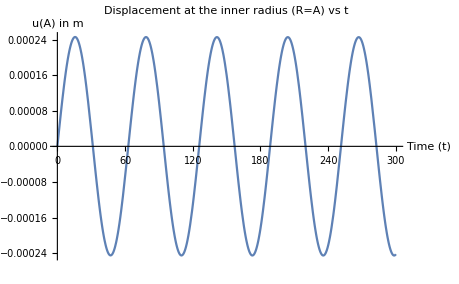

```mathematica
Plot[A*P1/.{R-> A},{t,0,300},PlotLabel->"Displacement at the inner radius (R=A) vs t",LabelStyle-> {14,GrayLevel[0]} ,AxesLabel->{"Time (t) ","u(A) in m"}]
```

##### Plot of the principle stretch f(A)

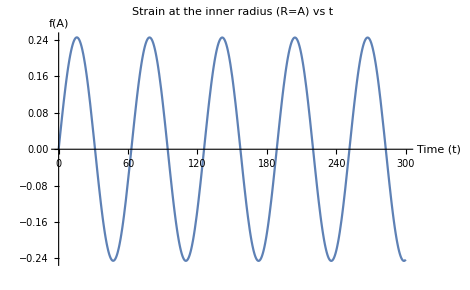

```mathematica
Plot[P1/.{R-> A},{t,0,300},PlotLabel->"Strain at the inner radius (R=A) vs t",LabelStyle-> {14,GrayLevel[0]} ,AxesLabel->{"Time (t) ","f(A)"}]
```

##### Plot of the Maximum Principle Stretch Rf’(R) + f(R) at R=A

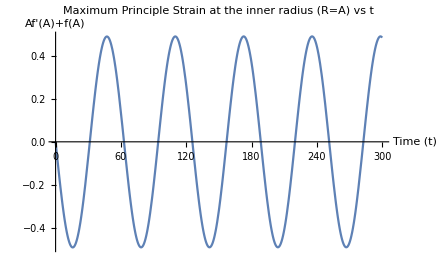

```mathematica
Plot[{R*D[P1,R]+P1}/.{R-> A},{t,0,300},PlotLabel->" Maximum Principle Strain at the inner radius (R=A) vs t",LabelStyle-> {14,GrayLevel[0]} ,AxesLabel->{"Time (t) ","Af'(A)+f(A)"}]
```

```mathematica
D[P1,R]
```

{(0.000025025 (0.0588235 ⅇ^(-0.166667 t) R^2+(8.64214×10^-8+0. ⅈ) (-680659. R^2 Cos[0.1 t]+4.22009×10^6 R^2 Sin[0.1 t])))/R^3-(0.0000750751 (1.90404×10^-8 ⅇ^(-0.00980392 t)+0.0196078 ⅇ^1 R^3+(8.64214×10^-8+0. ⅈ) (4+1.4067×10^6 R^3 1)))/R^4}
 |  |  |  |